### Constants

```mathematica
ClearAll["Global`*"]
```

```mathematica
h=6.626 10^-34;ℏ=h/(2 π);
μB=9.27400915*10^-24;
kb=1.38066 10^-23;
c=299792458; g=9.81;
g=9.8;
μm=10^-6;
```

### Potential options

```mathematica
{{RadioButton[Dynamic[{m,λ0,ω0,Γ}],{87 1.67 10^-27,(2/(3 780.0*10^-9)+1/(3 795*10^-9))^-1,(2*π*c)/((2/(3 780.0*10^-9)+1/(3 795*10^-9))^-1),2*π*6.1*10^6}], "Rb"},{RadioButton[Dynamic[{m,λ0,ω0,Γ}],{23 1.67 10^-27,(2/(3 589.158*10^-9)+1/(3 589.755 *10^-9))^-1,(2*π*c)/((2/(3 589.158*10^-9)+1/(3 589.755 *10^-9))^-1),2*π*9.76*10^6}] ,"Na"}}//Grid
```

| Rb
 | Na

```mathematica
{{Checkbox[Dynamic[λ1],{0,1}],"Left OT"},{Checkbox[Dynamic[λ2],{0,1}],"Right OT"},{Checkbox[Dynamic[λ4],{0,1}],"QT"},{Checkbox[Dynamic[λ5],{0,1}],"Gravity"}}//Grid
```

| Left OT
 | Right OT
 | QT
 | Gravity

```mathematica
{{RadioButton[Dynamic[{θ01,θ12,θ03}],{90°,180°,90°}], "View from CCD"},{RadioButton[Dynamic[{θ01,θ12,θ03}],{51°,157°,141°}] ,"View from new CCD"}}//Grid
(* θ01: Angle (in degrees) between F=2 Probe and 1^st pass *)
(* θ12: Angle (in degrees) between 1^st pass and 2^nd pass *)
```

| View from CCD
 | View from new CCD

### 946nm OT parameters

```mathematica
λ1070=947*10^-9;ω1070=(2*π*c)/λ1070;cvl=0.22;
powerL=0.18
reduction1=1;

w10x=57*10^-6;   (*left beam waist measured Nov. 09, 2015*)
w10y=57*10^-6;   (*left beam waist measured Nov. 09, 2015*)

Xoffset=-0*10^-6;
Zoffset=-0*10^-6;

w1x[z_]:=w10x*(1+((λ1070*(z-0 0.85 10^-3)1.007)/(π*w10x^2))^2)^(1/2);
w1y[z_]:=w10y*(1+((λ1070*(z+0 0.85 10^-3)0.939)/(π*w10y^2))^2)^(1/2);

Int1[x_,y_,z_]:=(2 powerL reduction1)/(π*w1x[z]*w1y[z])*Exp[-(2*x^2)/w1x[z]^2 -(2*y^2)/w1y[z]^2];
```

0.18

```mathematica
N@√(185*205)
```

194.743

### 946nm OT parameters

```mathematica
λ946=946*10^-9;ω946=(2*π*c)/λ946;cvr=0.13;
powerR=0.18
reduction2=1;

w20x=57*10^-6  ;  (*right beam waist measured Nov. 9, 2015*)
w20y=57*10^-6  ;  (*right beam waist measured Nov. 9, 2015*)

w2x[z_]:=w20x*(1+((λ946*(z-0 10^-3)0.999)/(π*w20x^2))^2)^(1/2);
w2y[z_]:=w20y*(1+((λ946*(z+0 10^-3)0.961)/(π*w20y^2))^2)^(1/2);

Int2[x_,y_,z_]:=(2 powerR reduction2)/(π*w2x[z]*w2y[z])*Exp[-(2*x^2)/w2x[z]^2 -(2*y^2)/w2y[z]^2];
```

0.18

### Trap potential

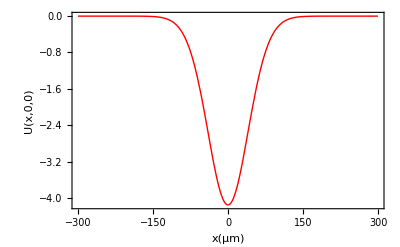

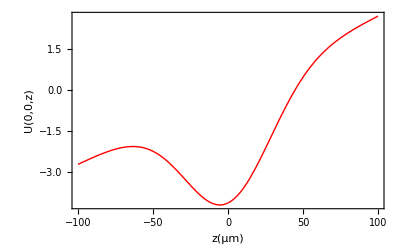

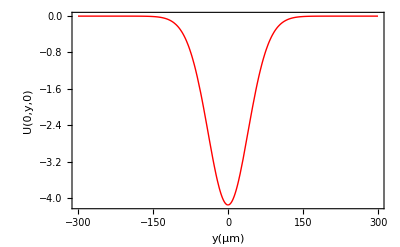

-Graphics3D-

```mathematica
YoffsetL=0μm;
YoffsetR=-0μm;
u1[x_,y_,z_]:=-10^6(3*π*c^2*Γ)/(2*ω0^3)*(1/(ω0-ω1070)+1/(ω0+ω1070))Int1[-(z-Zoffset) Sin[θ01]+(x-Xoffset) Cos[θ01],y-YoffsetL,(z-Zoffset) Cos[θ01]+(x-Xoffset) Sin[θ01]]/kb;
u2[x_,y_,z_]:=-10^6(3*π*c^2*Γ)/(2*ω0^3)*(1/(ω0-ω946)+1/(ω0+ω946))Int2[-(z-Zoffset) Sin[θ03]+(x-Xoffset) Cos[θ03],y-YoffsetR,(z-Zoffset) Cos[θ03]+(x-Xoffset) Sin[θ03]]/kb;
uQT[x_,y_,z_]:=0.5 10^6 7.5/7.5 1.6 μB √(((x-0μm)^2+(z-0μm)^2)/4+y^2)/kb ;
ug[y_]:=10^6*m*g*y/kb*1;

utot[x_,y_,z_]:=λ1 u1[x,y,z] +λ2 u2[x,y,z]+λ4 uQT[x,y,z]+λ5 ug[y];
Plot[{utot[x μm,0,0]},{x,-300,300},PlotRange->All,Frame->True,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Green}},FrameLabel->{"x(μm)","U(x,0,0)"}]
Plot[{utot[0,y μm,0]},{y,-100,100},PlotRange->All,Frame->True,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Green}},FrameLabel->{"z(μm)","U(0,0,z)"}]
Plot[{utot[0,0,z μm]},{z,-300,300},PlotRange->All,Frame->True,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Green}},FrameLabel->{"y(μm)","U(0,y,0)"}]
Plot3D[utot[x μm, y μm, 0 μm],{x,-300,300},{y,-300,300}]
```

### Frequencies and trap depth

```mathematica
sss=D[utot[x,y μm,z], y]/.{x->0,z->0};
soly=NSolve[Normal[Series[sss,{y,0,2}]]==0,y]
soly=FindRoot[Evaluate[sss]==0,{y,0}]
soly[[1,2]] μm
JocobM=1/m({{D[D[utot[x,y,z], x], x]*kb/10^6, D[D[utot[x,y,z], y], x]*kb/10^6, D[D[utot[x,y,z], z], x]*kb/10^6}, {D[D[utot[x,y,z], x], y]*kb/10^6, D[D[utot[x,y,z], y], y]*kb/10^6, D[D[utot[x,y,z], z], y]*kb/10^6}, {D[D[utot[x,y,z], x], z]*kb/10^6, D[D[utot[x,y,z], y], z]*kb/10^6, D[D[utot[x,y,z], z], z]*kb/10^6}})/.{x->0,z->0,y->soly[[1,2]] μm}
Freq=(Eigenvalues[JocobM])^0.5/(2π)
SpindleDirection=Eigenvectors[JocobM]
ArcTan[SpindleDirection[[2,1]]/SpindleDirection[[2,3]]]/π 180
```

{{y→-5.3312}}

{y→-5.42881}

-5.42881×10^-6

{{902730.,0.,590.593},{0.,1.73969×10^6,0.},{590.593,0.,902479.}}

{209.921,151.257,151.155}

{{0.,-1.,0.},{0.777146,0.,0.62932},{-0.62932,0.,0.777146}}

51.

### Distribution of atoms

```mathematica
Freq={60,230,60};
Tthermal=150 10^-9;
a0=0.52917720859*10^-10;
abf=66.77a0;
```

```mathematica
{{RadioButton[Dynamic[{Num,ωx,ωy,ωz,a}],{200000,2π Freq[[2]],2π Freq[[1]],2π Freq[[3]],106 a0}], "Rb"},{RadioButton[Dynamic[{Num,ωx,ωy,ωz,a}],{350000,2π Freq[[2]],2π Freq[[1]],2π Freq[[3]],68a0}] ,"Na"}}//Grid
```

| Rb
 | Na

```mathematica
{{RadioButton[Dynamic[{a1,a2}],{1,0}], "Thermal"},{RadioButton[Dynamic[{a1,a2}],{0,1}] ,"BEC"}}//Grid
```

| Thermal
 | BEC

```mathematica
ω̄=(ωx ωy ωz)^(1/3);
ā=√(ℏ/(m ω̄));
μ=15^(2/5)/2((Num a)/(ā))^(2/5)ℏ ω̄;
Rx=√((2 μ)/(m ωx^2))
Ry=√((2 μ)/(m ωy^2))
Rz=√((2 μ)/(m ωz^2))
U0=(4π a ℏ^2)/m;
n0=(2 μ)/(2U0)
gbf=(2π abf ℏ^2)/(3.0189488320987865*^-26);
σx=√((2 kb Tthermal)/(m ωx^2))
σy=√((2 kb Tthermal)/(m ωy^2))
σz=√((2 kb Tthermal)/(m ωz^2))
n0t=Num/((π)^(3/2)σx σy σz)
ygRb=g*(1/(2π 208.74119948933844)^2);
ygNa=g*(1/(2π 206.5706260235947)^2);
DensityDistributionRb[a1_,a2_,x_,y_,z_]:=a1 n0t ⅇ^(-(x/σx)^2)ⅇ^(-((y-ygRb)/σy)^2)ⅇ^(-(z/σz)^2)+  a2 n0(1-(x/Rx)^2-((y-ygRb)/Ry)^2-(z/Rz)^2);
DensityDistributionNa[a1_,a2_,x_,y_,z_]:=a1 n0t ⅇ^(-(x/σx)^2)ⅇ^(-((y-ygNa)/σy)^2)ⅇ^(-(z/σz)^2)+  a2 n0(1-(x/Rx)^2-((y-ygNa)/Ry)^2-(z/Rz)^2);
DensityDistributionRb[a1,a2,x,y,z]
DensityDistributionNa[a1,a2,x,y,z]
```

3.10561×10^-6

0.0000119048

0.0000119048

2.712×10^20

3.69469×10^-6

0.000014163

0.000014163

4.84637×10^19

0.+4.84637×10^19 ⅇ^(-7.3256×10^10 x^2-4.98528×10^9 (-5.69705×10^-6+y)^2-4.98528×10^9 z^2)

0.+4.84637×10^19 ⅇ^(-7.3256×10^10 x^2-4.98528×10^9 (-5.8174×10^-6+y)^2-4.98528×10^9 z^2)

```mathematica
RbDensity=Compile[{{x,_Real},{y,_Real},{z,_Real}},(1+Sign[#])#&[7.3465020394665755*^19 (1-3.1526586295729425*^11 x^2-3.3911731612610266*^11 (-5.697049455353749*^-6+y)^2-1.4172011432490384*^7 z^2)]];
```

```mathematica
NaDensity=Compile[{{x,_Real},{y,_Real},{z,_Real}},2.4383089900767656*^16 ⅇ^(-1.5621875692907595*^10 x^2-1.6803749407375711*^10 (-5.817403764736883*^-6+y)^2-702243.4932856017 z^2) Exp[-(gbf*RbDensity[x,y,z])/(kb*Tthermal)]];
```

```mathematica
Plot[{RbDensity[x μm ,ygRb ,0],NaDensity[x μm ,ygNa ,0]},{x,-10,10},PlotRange->{0,1.5 10^20},Frame->True,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Green}},FrameLabel->{"x(μm)","U(x,0,0)"}]
Plot[{RbDensity[0 μm ,y μm ,0],NaDensity[0 μm ,y μm ,0]},{y,-50,50},PlotRange->{0,3 10^17},Frame->True,PlotStyle->{{Thick,Red},{Thick,Black},{Thick,Green}},FrameLabel->{"y(μm)","U(y,0,0)"}]
```

-Graphics-

-Graphics-

```mathematica
xx=Solve[RbDensity[x μm,ygRb,0]==2 10^20,x];
yy=Solve[RbDensity[0,y μm,0]==2 10^20,y];
zz=Solve[RbDensity[0,ygRb,z μm]==2 10^20,z];
NIntegrate[NaDensity[x μm,y μm,z μm],{x,xx[[1,1,2]],xx[[2,1,2]]},{y,yy[[1,1,2]],yy[[2,1,2]]},{z,zz[[1,1,2]],zz[[2,1,2]]}]/NIntegrate[NaDensity[x μm,y μm,z μm],{x,-10,10},{y,-10,10},{z,-10,10}]
```

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

CompiledFunction::cfsa: Argument y/1000000 at position 2 should be a machine-size real number.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

CompiledFunction::cfsa: Argument z/1000000 at position 3 should be a machine-size real number.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

-1.55393×10^-12+0.239618 ⅈ

```mathematica
values=Rescale[Table[NaDensity[x μm,y μm,z μm],{x,-20,20,1},{y,-10,30,1},{z,-2000,2000,10}]];
Graphics3D[Raster3D[values,ColorFunction->"HueOpacity"],Axes->True]
```

-Graphics3D-

```mathematica
values2=Rescale[Table[RbDensity[ x μm,y μm,z μm],{x,-3,3,.1},{y,3,9,.1},{z,-250,250,1}]];
Graphics3D[Raster3D[values2,ColorFunction->"HueOpacity"],Axes->True]
```

-Graphics3D-

```mathematica
PolarNaDensity[ρ_]:=NaDensity[(√3)/3 ρ,(√3)/3 Rx/Ry ρ+ygRb,(√3)/3 Rx/Rz ρ]
OdNaDensity[r_]:=NIntegrate[(PolarNaDensity[ρ]ρ)/(√(ρ^2-r^2)),{ρ,1.0001r,Infinity}]-NIntegrate[(PolarNaDensity[ρ]ρ)/(√(ρ^2-r^2)),{ρ,-Infinity,-1.0001r}]
ODNaDensity=Compile[{{y,_Real},{z,_Real}},NIntegrate[NaDensity[x μm,y+ygRb,z],{x,-Infinity,Infinity},WorkingPrecision->MachinePrecision]];
```

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
ODImage2=ParallelTable[ODNaDensity[y μm,z μm],{y,-10,10,0.5},{z,-12,12,0.5}];//AbsoluteTiming
ImageAdjust@Image[ODImage2]
(*Graphics[Raster[ODImage]]*)
```

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

CompiledFunction::cfsa: Argument x/1000000 at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

{19.0581,Null}

-Graphics-

```mathematica
Dimensions@ODImage2
```

{41,49}

```mathematica
ODImage=ODImage2[[23;;41,All]];
```

```mathematica
ReverseNaDensity[r_,z_]:=-1/π∑_(n=1)^(18-2r) (ODImage[[n+2r+1,2z]]-ODImage[[n+2r,2z]])/(√((2 r+n)^2-(2r)^2))
```

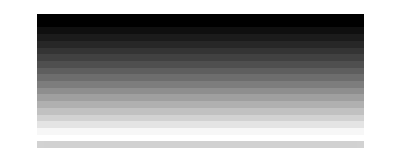

-Graphics3D-

```mathematica
ReverseNaDensityTable=Rescale[Table[ReverseNaDensity[r,z],{r,0,9.5,0.5},{z,0.5,24.5,0.5}]];
Graphics[Raster[ReverseNaDensityTable]]
ListPlot3D[Rescale[Table[ReverseNaDensity[r,z],{r,0,9.5,0.5},{z,0.5,24.5,0.5}]],PlotRange->All]
```

```mathematica
ListPlot3D[Rescale[Table[NaDensity[0 μm,r μm+ygNa,z μm],{r,0,9.5,0.5},{z,-12,12,0.5}]]]
```

-Graphics3D-

```mathematica
OD=Table[Re[OdNaDensity[r μm]],{r,0,4.5,0.01}]
ListLinePlot[OD]
```

CompiledFunction::cfsa: Argument ρ/(√3) at position 1 should be a machine-size real number.

NIntegrate::inumr: The integrand (2.43831×10^16 ⅇ^(«1») ρ)/(√(0.+ρ^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

CompiledFunction::cfsa: Argument ρ/(√3) at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

NIntegrate::inumr: The integrand (2.43831×10^16 ⅇ^(«1») ρ)/(√(0.+ρ^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0.}}.

NIntegrate::inumr: The integrand (2.43831×10^16 ⅇ^(«1») ρ)/(√(0.+ρ^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

ListLinePlot::lpn: OD is not a list of numbers or pairs of numbers.

ListLinePlot[OD]

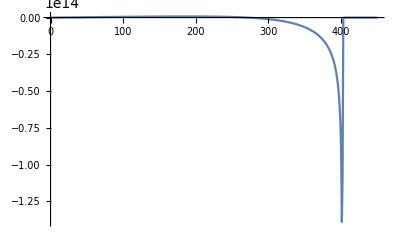

```mathematica
dOD=Table[100 (OD[[i+1]]-OD[[i]]),{i,1,450}];
ListLinePlot[dOD,PlotRange->All]
```

```mathematica
RpolarNaDensity[r_]:=-Sum[(dOD[[ρ]]*0.01/(√((ρ/100)^2-r^2))),{ρ,100.01r,450}]
```

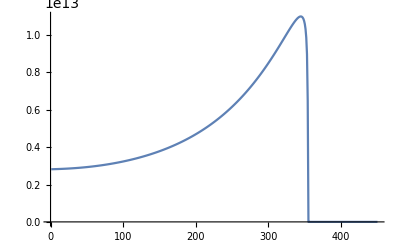

```mathematica
RDensity=Table[RpolarNaDensity[r],{r,0,4.49,0.01}];
ListLinePlot[RDensity,PlotRange->All]
```

```mathematica
0.01/3.14 180
```

0.573248